Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

```mathematica
Clear["Global`*"]
```

1 - 7 Contour integration. Unit Circle
Integrate counterclockwise around the unit circle.

1.  ∮_C Sin[z]/z^4 ⅆz

```mathematica
Clear["Global`*"]
```

This problem is in the s.m., and I will use it. The explanation in the s.m. clarifies the procedure. Although I am looking at an integral symbol, there is really no integrating to be done in the normal sense of the term. On numbered line (1) of p. 664 of the text is the formula I will be working with, namely
f^(n)(z_0)==(n!)/(2 π ⅈ)∮_C f[z]/(z-z_0)^(n+1)ⅆz
and rearranging and filling in parts of this equation will result in the answer to the problem. First step is to get the ‘integral’ term by itself

(2 π ⅈ)/(n!)f^(n)(z_0)=∮_C f[z]/(z-z_0)^(n+1)ⅆz

At this point, looking back and forth between the numbered line (1) ‘integral’ and the problem ‘integral’, I can identify components. Thus

```mathematica
f[z_]=Sin[z]
```

Sin[z]

Likewise, z^4==(z-z_0)^(n+1), implying that z_0==0 and n==3. So now I can identify

```mathematica
Subscript[z, 0]=0
```

0

```mathematica
f'''[z]
```

-Cos[z]

and

```mathematica
f'''[Subscript[z, 0]]
```

-1

So now all I need to do is put the lhs together

```mathematica
(2π ⅈ)/(3!)f'''[Subscript[z, 0]]
```

-(ⅈ π)/3

The green cell matches the text answer. This is not difficult. I just need to remember that I am seeking the lhs, not the right. One thing I need to remember is that f[z] needs to be analytic for this procedure to work. No problem so far with that.

3.  ∮_C Exp[z]/z^n ⅆz , n=1,2,...

```mathematica
Clear["Global`*"]
```

Same drill. Putting the working form of the numbered line (1) equation in here for reference:
(2 π ⅈ)/(n!)f^(n)(z_0)=∮_C f[z]/(z-z_0)^(n+1)ⅆz

```mathematica
f[z_]=Exp[z]
```

ⅇ^z

And z^n==(z-z_0)^(n+1),  implying that z_0==0 and n==n+1. What? How will I handle this? Pretty clear that I will have to do it one n-value at a time. So suppose I take n (in the problem integral) to be 3. Then n (in the template integral) will be 2. So I can write

```mathematica
Subscript[z, 0]=0
```

0

```mathematica
f''[z]
```

ⅇ^z

and

```mathematica
f''[Subscript[z, 0]]
```

1

Putting the lhs together,

```mathematica
(2 π ⅈ)/(2!)f''[Subscript[z, 0]]
```

ⅈ π

The text answer is the general sol’n, but yields the green cell when n=3. I could write the general sol’n too, ((2 π ⅈ)/((n-1)!))ⅇ^0.

```mathematica
hf=HoldForm[Series[(2 ⅈ π)/((-1+n)!),{n,0,4}]]
```

Series[(2 ⅈ π)/((-1+n)!),{n,0,4}]

Except this doesn’t really give me what I want. I don’t know how to make a series that looks like what I want.

5.  ∮_C Cosh[2 z]/(z-1/2)^4 ⅆz

```mathematica
Clear["Global`*"]
```

Pasting in the target expression again
(2 π ⅈ)/(n!)f^(n)(z_0)=∮_C f[z]/(z-z_0)^(n+1)ⅆz
so that

```mathematica
f[z_]=Cosh[2 z]
```

Cosh[2 z]

and  (z-1/2)^4==(z-z_0)^(n+1) implies that z_0=1/2and n==3

```mathematica
Subscript[z, 0]=1/2
```

1/2

```mathematica
(2 π ⅈ)/(3!)f'''[Subscript[z, 0]]
```

8/3 ⅈ π Sinh[1]

```mathematica
N[%]
```

0.+9.84534 ⅈ

The green cells above match the text answer.

7.  ∮_C Cos[z]/z^(2n+1)ⅆz , n=0,1,...

```mathematica
Clear["Global`*"]
```

The target expression in this case is confusing, because the n on the left is not the n on the right 
(2 π ⅈ)/(n!)f^(n)(z_0)=∮_C f[z]/(z-z_0)^(n+1)ⅆz
so that

```mathematica
f[z_]=Cos[z]
```

Cos[z]

and z^(2 n+1) = (z-z_0)^(m+1) , which implies that z_0=0 and

```mathematica
Solve[2 n+1==m+1,m]
```

{{m→2 n}}

The way this is set up, both m and n need to be integers. To restate the target
(2 π ⅈ)/((2n)!)f^(2n)(z_0)=∮_C f[z]/(z-z_0)^(m+1)ⅆz
Here m can only be even, but calculations are not done on the right, but rather the left.

```mathematica
Subscript[z, 0]=0
```

0

```mathematica
f[Subscript[z, 0]]
```

1

```mathematica
(2 π ⅈ)/(0!)f[Subscript[z, 0]]/.f[Subscript[z, 0]]->1 (* for n=0 *)
```

2 ⅈ π

```mathematica
(2 π ⅈ)/((2 1)!)f''[Subscript[z, 0]] (* for n=1 *)
```

-ⅈ π

```mathematica
(2 π ⅈ)/((2 2)!)f''''[Subscript[z, 0]] (* for n=2 *)
```

(ⅈ π)/12

```mathematica
(2 π ⅈ)/((2 3)!)f''''''[Subscript[z, 0]] (* for n=3 *)
```

-(ⅈ π)/360

```mathematica
(2 π ⅈ)/((2 4)!)f''''''''[Subscript[z, 0]] (* for n=4 *)
```

(ⅈ π)/20160

```mathematica
dirk[n_,N_,z_]=Sequence[(2 π ⅈ)/((2 n)!)D[f[z],{z,2n}],{n,N,N}]
```

Sequence[(2 ⅈ π Cos^(2 n)[z])/((2 n)!),{n,N,N}]

```mathematica
dirk[0,0,0]
```

Sequence[2 ⅈ π,{0,0,0}]

```mathematica
dirk[3,3,0]
```

Sequence[-(ⅈ π)/360,{3,3,3}]

```mathematica
dirk[4,4,0]
```

Sequence[(ⅈ π)/20160,{4,4,4}]

8 - 19 Integration. Different contours
Integrate.

9.  ∮_C Tan[π z]/z^2 ⅆz , C the ellipse 16 x^2+y^2==1 clockwise

```mathematica
Clear["Global`*"]
```

```mathematica
p1=Plot[y/.Solve[(x/4)^2+ (y)^2==1],{x,-4,4},AspectRatio->Automatic,ImageSize->250,AxesLabel->{"Re","Im"},GridLines->Automatic,PlotRange->{-2,2}];
```

```mathematica
p2=Plot[Tan[π z],{z,-4,4}];
```

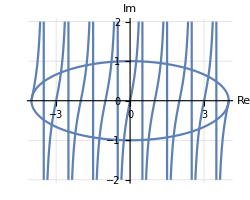

```mathematica
Show[p1,p2]
```

By looking at the plot, the tangent’s asymptotes, which will be the location of its nonanalyticities, are all outside the elliptic domain of interest. There does remain the origin, however, as the point of difficulty. Recasting numbered line (1’) of p. 646,
2π ⅈ(f'[z_0])== ∮_C f[z]/(z-z_0)^2 ⅆz
gives me the working target. Again z_0 will equal 0.

```mathematica
Subscript[z, 0]=0
```

0

```mathematica
f[z_]=Tan[π z]
```

Tan[π z]

```mathematica
f'[z]
```

π Sec[π z]^2

```mathematica
f'[Subscript[z, 0]]
```

π

```mathematica
2π ⅈ(f'[Subscript[z, 0]])
```

2 ⅈ π^2

The s.m. tips me off to a gotcha. Boxed theorem 1, p. 664, which includes numbered line (1'), applies to curves integrated in the counterclockwise direction along their paths. The current problem specifies a clockwise direction of travel, meaning that I have to negate the result to get the correct answer.

```mathematica
-2π ⅈ(f'[Subscript[z, 0]])
```

-2 ⅈ π^2

11.  ∮_C ((1+z)Sin[z])/(2z-1)^2 ⅆz , C:|z-ⅈ|==2 counterclockwise

```mathematica
Clear["Global`*"]
```

Again reminding myself of the circle formula: ParametricPlot[{r Cos[t] + a, r Sin[t] + b}, {t, 0, 2 π}

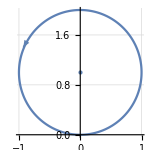

```mathematica
ParametricPlot[{1 Cos[z], 1 Sin[z]+1},{z,0,2 π},ImageSize->150,GridLines->Automatic,Epilog->{{RGBColor[95/255,130/255,179/255],Arrowheads[0.1],Arrow[{{-0.87,1.5},{-0.93,1.4}}]},{RGBColor[95/255,130/255,179/255],Point[{0,1}]}}]
```

I believe that 2π ⅈ(f'[z_0])== ∮_C f[z]/(z-z_0)^2 ⅆz
can be retained as the working target. This time z_0=1/2. The sine function is entire, and the polynomial (1+z) is nonthreatening, so I will assume analyticity for f[z].

```mathematica
f[z_]=(1+z)Sin[z]
```

(1+z) Sin[z]

```mathematica
Subscript[z, 0]=1/2
```

1/2

```mathematica
f'[z]
```

(1+z) Cos[z]+Sin[z]

```mathematica
f'[Subscript[z, 0]]
```

3/2 Cos[1/2]+Sin[1/2]

```mathematica
2π ⅈ(f'[Subscript[z, 0]])
```

2 ⅈ π (3/2 Cos[1/2]+Sin[1/2])

```mathematica
Simplify[%]
```

ⅈ π (3 Cos[1/2]+2 Sin[1/2])

```mathematica
N[%]
```

0.+11.2833 ⅈ

A strange outcome. Though the symbolic result matches the answer in the text, the numerical result does not. Seems too simple to misread it. WolframAlpha gives the same answer as shown in yellow.

13.  ∮_C Log[z]/(z-2)^2 ⅆz , C:|z-3|==2 counterclockwise

```mathematica
Clear["Global`*"]
```

```mathematica
p1=ParametricPlot[{2 Cos[z]+3, 2 Sin[z]+0},{z,0,2 π},ImageSize->150,GridLines->Automatic,Epilog->{{RGBColor[95/255,130/255,179/255],Arrowheads[0.1],Arrow[{{1.213,0.9},{1.15,0.8}}]},{RGBColor[95/255,130/255,179/255],Point[{2,0}]}}];
```

```mathematica
p2=Plot[Log[z],{z,0,5}];
```

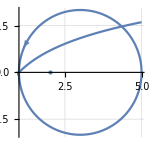

```mathematica
Show[p1,p2]
```

The log function is analytic on any open set of its domain.

I believe that 2π ⅈ(f'[z_0])== ∮_C f[z]/(z-z_0)^2 ⅆz
can be retained as the working target. This time z_0=2.

```mathematica
f[z_]=Log[z]
```

Log[z]

```mathematica
Subscript[z, 0]=2
```

2

```mathematica
f'[z]
```

1/z

```mathematica
f'[Subscript[z, 0]]
```

1/2

```mathematica
2π ⅈ(f'[Subscript[z, 0]])
```

ⅈ π

15.  ∮_C Cosh[4 z]/(z-4)^3 ⅆz , C consists of |z|==6 counterclockwise and |z-3|=2 clockwise

```mathematica
Clear["Global`*"]
```

```mathematica
p1=ParametricPlot[{{6 Cos[z]+0, 6 Sin[z]+0},{2 Cos[z]+3, 2 Sin[z]+0}},{z,0,2 π},ImageSize->150,GridLines->Automatic,Epilog->{{RGBColor[95/255,130/255,179/255],Arrowheads[0.1],Arrow[{{-4.25,4.2},{-4.47,4.0}}]},{RGBColor[40/255,40/255,230/255],PointSize[0.04],Point[{2,0}]},{RGBColor[223/255,155/255,52/255],Arrowheads[0.085],Arrow[{{2.15,1.75},{2.48,1.95}}]}}];
```

```mathematica
p2=Plot[Cosh[4 z],{z,-6,6}];
```

```mathematica
p3=Graphics[Line[{{2,5},{-2,5},{-4,3.75},{-5,0.5},{0.5,0.5},{1,2},{3,2.5},{4.5,2.5},{2,5}}]];
```

```mathematica
p4=Graphics[Line[{{-5,-0.5},{0.5,-0.5},{1,-2},{3,-2.5},{4.5,-2.5},{2,-5},{-2,-5},{-4,-3.75}}]];
```

```mathematica
p5=Graphics[{{Arrowheads[0.085],Arrow[{{-4,-3.75},{-5,-0.5}}]},{Arrowheads[0.085],Arrow[{{-4,3.75},{-5,0.5}}]}}];
```

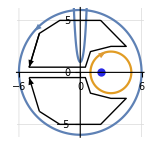

```mathematica
Show[p1,p2,p3,p4,p5]
```

According to Wikipedia, the (complex) hyperbolic cosine is holomorphic, which I believe means it is also analytic.

I will leave 2π ⅈ(f'[z_0])== ∮_C f[z]/(z-z_0)^2 ⅆz as the working target. The z_0 I will set as 2, and pull a squared term out as part of the function f[z].

```mathematica
f[z_]=Cosh[4 z]/(z-4)^2
```

Cosh[4 z]/(-4+z)^2

```mathematica
Subscript[z, 0]=2
```

2

```mathematica
f'[z]
```

-(2 Cosh[4 z])/(-4+z)^3+(4 Sinh[4 z])/(-4+z)^2

```mathematica
f'[Subscript[z, 0]]
```

Cosh[8]/4+Sinh[8]

```mathematica
2π ⅈ(f'[Subscript[z, 0]])
```

2 ⅈ π (Cosh[8]/4+Sinh[8])

I would propose the yellow cell as the answer if only the teal and not the orange domain was in the problem. But as explained on http://www.math.unm.edu/~nitsche/courses/313/s16/lec19_int5.pdf, the orange domain makes a difference. Essentially, working the problem can be done using the Cauchy-Goursat theorem, which involves branch cuts. One path around the branch cuts is counterclockwise and the other is clockwise, and a difference in sign makes them cancel out, giving a total of 0, which is what the text reports. Rough paths are shown in the sketch.

17.  ∮_C (ⅇ^-z Sin[z])/(z-4)^3 ⅆz , C consists of |z|==5 counterclockwise and |z-3|==3/2 clockwise

This one is somewhat similar to the last. The text answer for this problem quotes numbered line (6) in section 14.2. This deals with Cauchy’s integral theorem for doubly connected domains. However, in that section it was specifically stated that both paths had the same orientation. In this problem the orientations of inner and outer path are opposite. Again, http://www.math.unm.edu/~nitsche/courses/313/s16/lec19_int5.pdf does give some support for zero total integral value, again, making use of Cauchy-Goursat. As for analyticity, Wikipedia vouches for the exponential function and the trig functions.

19.  ∮_C ⅇ^(3 z)/(4z-π ⅈ)^3 ⅆz , C: |z|==1 counterclockwise

```mathematica
Clear["Global`*"]
```

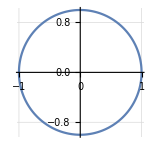

```mathematica
p1=ParametricPlot[{1 Cos[z]+0, 1 Sin[z]+0},{z,0,2 π},ImageSize->150,GridLines->Automatic]
```

I believe that (2 π ⅈ)/(n!)f^(n)(z_0)=∮_C f[z]/(z-z_0)^(n+1)ⅆz

can be retained as the working target. This time the function will be a little complicated. I need to calculate what n is equal to.

I need to try to unscramble the denominator,

(4z-π ⅈ)^3==(4z-π ⅈ)(4z-π ⅈ)==4(z-(π ⅈ)/4)4(z-(π ⅈ)/4)4(z-(π ⅈ)/4)==4^3(z-(π ⅈ)/4)^3

I can pull the 4^3 out of the denominator and modify the coefficient accordingly

```mathematica
coef=(2 π ⅈ)/(4^3 n!)
```

(ⅈ π)/(32 n!)

Looking at what I have left, n=2 and z_0=(π ⅈ)/4,

```mathematica
Subscript[z, 0]=(π ⅈ)/4
```

(ⅈ π)/4

```mathematica
coef=coef/.n->2
```

(ⅈ π)/64

And inside the integral, the numerator is the function,

```mathematica
f[z_]=ⅇ^(3 z)
```

ⅇ^(3 z)

```mathematica
f''[z]
```

9 ⅇ^(3 z)

Since n=2, I want the second derivative of z_0,

```mathematica
f''[Subscript[z, 0]]
```

9 ⅇ^(3 z_0)

```mathematica
coef f''[Subscript[z, 0]]
```

9/64 ⅈ ⅇ^((3 ⅈ π)/4) π

The green cell above matches the text answer, but the text then recasts it.

```mathematica
ans=(-9π(1+ⅈ))/(64 √2)
```

-((9/64+(9 ⅈ)/64) π)/(√2)

```mathematica
FullSimplify[%]
```

-9/64 (-1)^(1/4) π

The answers agree if

```mathematica
-(-1)^(1/4)==ⅈ ⅇ^((3 ⅈ π)/4)
```

True

```mathematica
FullSimplify[ⅈ ⅇ^((3 ⅈ π)/4)]
```

-(-1)^(1/4)